```mathematica
JUAN FRANCISCO ABAN FONTECHA
DNI:77365843F
Dia: 03/11/2014
```

```mathematica
19.En el conjunto A={1,2,3,4} se establece la relación binaria
R={(1,1),(2,2),(2,3),(2,4),(3,2),(3,3),(3,4),(4,2),(4,3),(4,4)}
Justificar que es una relación de equivalencia y calcular el conjunto cociente.
```

```mathematica
A={1,2,3,4};
R={{1,1},{2,2},{2,3},{2,4},{3,2},{3,3},{3,4},{4,2},{4,3},{4,4}};
Reflexiva=True;For[n=1,n≤Length[A],n++,If[Intersection[{{A[[n]],A[[n]]}},R]=={{A[[n]],A[[n]]}},Null,Reflexiva=False]];Simetrica=True;For[m=1,m≤Length[R],m++,If[Intersection[{{R[[m,2]],R[[m,1]]}},R]=={{R[[m,2]],R[[m,1]]}},Null,Simetrica=False]];
Transitiva=True;For[p=1,p≤Length[R],p++,For[q=1,q≤Length[R],q++,If[R[[p,1]]==R[[q,2]],If[Intersection[{{R[[q,1]],R[[p,2]]}},R]=={{R[[q,1]],R[[p,2]]}},Null,Transitiva=False]];];];Antisimetrica=True;For[r=1,r≤Length[R],r++,If[Intersection[{{R[[r,2]],R[[r,1]]}},R]=={{R[[r,2]],R[[r,1]]}}&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),Antisimetrica=False]];If[Reflexiva,Print["R es reflexiva"],Print["R no es reflexiva"]]If[Simetrica,Print["R es simétrica"],Print["R no es simétrica"]]If[Transitiva,Print["R es transitiva"],Print["R no es transitiva"]]If[Antisimetrica,Print["R es antisimétrica"],Print["R no es antisimétrica"]];If[Reflexiva&&Simetrica&&Transitiva,Print["R es una relación de equivalencia"],Print["R no es relación de equivalencia"]];If[Reflexiva&&Antisimetrica&&Transitiva,Print["R es una relación de orden"],Print["R no es relación de orden"]]
```

R es reflexiva

R es simétrica

R es transitiva

R no es antisimétrica

R es una relación de equivalencia

R no es relación de orden

```mathematica
COCIENTE[A_,R_]:=Module[{CONTADORi,CONTADORj,anadir},cociente={{A[[1]]}};
Do[
anadir=True;
Do[
If[Intersection[{{A[[CONTADORi]],cociente[[CONTADORj]][[1]]}},R]!={},
AppendTo[cociente[[CONTADORj]],A[[CONTADORi]]];
anadir=False;
Break[];
];
,{CONTADORj,1,Length[cociente]}];
If [anadir,
AppendTo[cociente,{A[[CONTADORi]]}];
];
,{CONTADORi,2,Length[A]}];
cociente
];
```

```mathematica
COCIENTE[A,R]
```

{{1},{2,3,4}}

```mathematica
24. Sea X={a,b,c,d,e,f} junto con la ordenación dada por el siguiente diagrama:
```

Diagrama de orden:

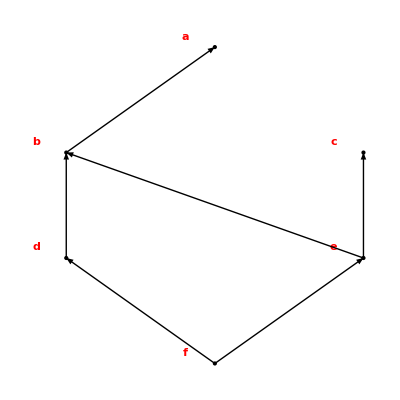

```mathematica
A={a,b,c,d,e,f};
R={{a,a},{b,b},{c,c},{d,d},{e,e},{f,f}, {f,e},{e,c},{f,c},{e,b},{e,a},{f,b},{b,a},{f,a},{f,d},{d,b},{d,a},{f,b}};
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];B=A;t1=1;nivel=0;While[B≠{},minimales={};nivel++;Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False],{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,
{n1,1,Length[B]}];
B=Complement[B,minimales];
]
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];R1={};
Do[
Do[
If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,
R1=Union[R1,{R[[k1]]}];
];
,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];Do[t1++;puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2),{k1,1,cont}],
{j1,1,tabla[[Length[A],1]]}];Coord[elem_]:=Do[If[elem==tabla[[h1,2]],
Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];Do[Coord[A[[i1]]],{i1,1,Length[A]}];Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];
,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

```mathematica
Sea Y={b,f,e} y Z={c,a,e,d} subconjuntos de X.Se pide:
d.Cotas superiores e inferiores de Y y de Z.¿Existen supremo e ínfimo?.
```

```mathematica
A={a,b,c,d,e,f};
B = {b,f,e} ;
R={{a,a},{b,b},{c,c},{d,d},{e,e},{f,f}, {f,e},{e,c},{f,c},{e,b},{f,b},{b,a},{f,a},{f,d},{d,b},{f,b}};
cotassuperiores={};Do[csuper=True;Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False],{m,1,Length[B]}];If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];If[cotassuperiores=={},Print["No hay cotas superiores"],Print["Cotas superiores: ",cotassuperiores];supremo={};Do[mini=True;Do[If[Intersection[{{cotassuperiores[[n]],cotassuperiores[[m]]}},R]=={},mini=False],{m,1,Length[cotassuperiores]}];If[mini,AppendTo[supremo,cotassuperiores[[n]]]];,{n,1,Length[cotassuperiores]}];If[supremo=={},Print["No tiene supremo"],Print["Supremo: ",supremo[[1]]]]];
```

Cotas superiores: {b}

Supremo: b

```mathematica
A={a,b,c,d,e,f};
B = {b,f,e} ;
R={{a,a},{b,b},{c,c},{d,d},{e,e},{f,f}, {f,e},{e,c},{f,c},{e,b},{f,b},{b,a},{f,a},{f,d},{d,b},{f,b}};
cotasinferiores={};Do[cinfer=True;Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False],{m,1,Length[B]}];If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];If[cotasinferiores=={},Print["No hay cotas inferiores"],Print["Cotas inferiores: ",cotasinferiores];infimo={};Do[maxi=True;Do[If[Intersection[{{cotasinferiores[[m]],cotasinferiores[[n]]}},R]=={},maxi=False],{m,1,Length[cotasinferiores]}];If[maxi,AppendTo[infimo,cotasinferiores[[n]]]];,{n,1,Length[cotasinferiores]}];If[infimo=={},Print["No tiene ínfimo"],Print["Ínfimo: ",infimo[[1]]]]];
```

Cotas inferiores: {f}

Ínfimo: f

```mathematica
A={a,b,c,d,e,f};
B = {c,a,e,d} ;
R={{a,a},{b,b},{c,c},{d,d},{e,e},{f,f}, {f,e},{e,c},{f,c},{e,b},{f,b},{b,a},{f,a},{f,d},{d,b},{f,b}};
cotassuperiores={};Do[csuper=True;Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False],{m,1,Length[B]}];If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];If[cotassuperiores=={},Print["No hay cotas superiores"],Print["Cotas superiores: ",cotassuperiores];supremo={};Do[mini=True;Do[If[Intersection[{{cotassuperiores[[n]],cotassuperiores[[m]]}},R]=={},mini=False],{m,1,Length[cotassuperiores]}];If[mini,AppendTo[supremo,cotassuperiores[[n]]]];,{n,1,Length[cotassuperiores]}];If[supremo=={},Print["No tiene supremo"],Print["Supremo: ",supremo[[1]]]]];
```

No hay cotas superiores

```mathematica
A={a,b,c,d,e,f};
B = {c,a,e,d} ;
R={{a,a},{b,b},{c,c},{d,d},{e,e},{f,f}, {f,e},{e,c},{f,c},{e,b},{f,b},{b,a},{f,a},{f,d},{d,b},{f,b}};
cotasinferiores={};Do[cinfer=True;Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False],{m,1,Length[B]}];If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];If[cotasinferiores=={},Print["No hay cotas inferiores"],Print["Cotas inferiores: ",cotasinferiores];infimo={};Do[maxi=True;Do[If[Intersection[{{cotasinferiores[[m]],cotasinferiores[[n]]}},R]=={},maxi=False],{m,1,Length[cotasinferiores]}];If[maxi,AppendTo[infimo,cotasinferiores[[n]]]];,{n,1,Length[cotasinferiores]}];If[infimo=={},Print["No tiene ínfimo"],Print["Ínfimo: ",infimo[[1]]]]];
```

Cotas inferiores: {f}

Ínfimo: f

```mathematica
e.Máximos y mínimos de Y y Z.
```

```mathematica
A={a,b,c,d,e,f};
B = {b,f,e} ;
R={{a,a},{b,b},{c,c},{d,d},{e,e},{f,f}, {f,e},{e,c},{f,c},{e,b},{f,b},{b,a},{f,a},{f,d},{d,b},{f,b}};
maximo={};Do[maxi=True;Do[If[Intersection[{{A[[m]],A[[n]]}},R]=={},maxi=False],{m,1,Length[A]}];If[maxi,AppendTo[maximo,A[[n]]]];,{n,1,Length[A]}];If[maximo=={},Print["No tiene máximo"],Print["Máximo: ",maximo[[1]]]]
```

No tiene máximo

```mathematica
A={a,b,c,d,e,f};
B = {b,f,e} ;
R={{a,a},{b,b},{c,c},{d,d},{e,e},{f,f}, {f,e},{e,c},{f,c},{e,b},{f,b},{b,a},{f,a},{f,d},{d,b},{f,b}};
minimo={};Do[mini=True;Do[If[Intersection[{{A[[n]],A[[m]]}},R]=={},mini=False],{m,1,Length[A]}];If[mini,AppendTo[minimo,A[[n]]]];,{n,1,Length[A]}];If[minimo=={},Print["No tiene mínimo"],Print["Mínimo: ",minimo[[1]]]]
```

Mínimo: f

```mathematica
A={a,b,c,d,e,f};
B = {c,a,e,d} ;
R={{a,a},{b,b},{c,c},{d,d},{e,e},{f,f}, {f,e},{e,c},{f,c},{e,b},{f,b},{b,a},{f,a},{f,d},{d,b},{f,b}};
maximo={};Do[maxi=True;Do[If[Intersection[{{A[[m]],A[[n]]}},R]=={},maxi=False],{m,1,Length[A]}];If[maxi,AppendTo[maximo,A[[n]]]];,{n,1,Length[A]}];If[maximo=={},Print["No tiene máximo"],Print["Máximo: ",maximo[[1]]]]
```

No tiene máximo

```mathematica
A={a,b,c,d,e,f};
B = {c,a,e,d} ;
R={{a,a},{b,b},{c,c},{d,d},{e,e},{f,f}, {f,e},{e,c},{f,c},{e,b},{f,b},{b,a},{f,a},{f,d},{d,b},{f,b}};
minimo={};Do[mini=True;Do[If[Intersection[{{A[[n]],A[[m]]}},R]=={},mini=False],{m,1,Length[A]}];If[mini,AppendTo[minimo,A[[n]]]];,{n,1,Length[A]}];If[minimo=={},Print["No tiene mínimo"],Print["Mínimo: ",minimo[[1]]]]
```

Mínimo: f

```mathematica
f.Elementos maximales y minimales de X,Y y Z.
```

```mathematica
A={a,b,c,d,e,f};
B = {b,f,e} ;
R={{a,a},{b,b},{c,c},{d,d},{e,e},{f,f}, {f,e},{e,c},{f,c},{e,b},{f,b},{b,a},{f,a},{f,d},{d,b},{f,b}};
maximales={};Do[maximal=True;Do[If[Intersection[{{A[[n]],A[[m]]}},R]≠{}&&n≠m,maximal=False],{m,1,Length[A]}];If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];Print["Maximales: ",maximales]
```

Maximales: {a,c}

```mathematica
A={a,b,c,d,e,f};
B = {b,f,e} ;
R={{a,a},{b,b},{c,c},{d,d},{e,e},{f,f}, {f,e},{e,c},{f,c},{e,b},{f,b},{b,a},{f,a},{f,d},{d,b},{f,b}};
minimales={};Do[minimal=True;Do[If[Intersection[{{A[[m]],A[[n]]}},R]≠{}&&n≠m,minimal=False],{m,1,Length[A]}];If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];Print["Minimales: ",minimales]
```

Minimales: {f}

```mathematica
A={a,b,c,d,e,f};
B = {c,a,e,d} ;
R={{a,a},{b,b},{c,c},{d,d},{e,e},{f,f}, {f,e},{e,c},{f,c},{e,b},{f,b},{b,a},{f,a},{f,d},{d,b},{f,b}};
maximales={};Do[maximal=True;Do[If[Intersection[{{A[[n]],A[[m]]}},R]≠{}&&n≠m,maximal=False],{m,1,Length[A]}];If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];Print["Maximales: ",maximales]
```

Maximales: {a,c}

```mathematica
A={a,b,c,d,e,f};
B = {c,a,e,d} ;
R={{a,a},{b,b},{c,c},{d,d},{e,e},{f,f}, {f,e},{e,c},{f,c},{e,b},{f,b},{b,a},{f,a},{f,d},{d,b},{f,b}};
minimales={};Do[minimal=True;Do[If[Intersection[{{A[[m]],A[[n]]}},R]≠{}&&n≠m,minimal=False],{m,1,Length[A]}];If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];Print["Minimales: ",minimales]
```

Minimales: {f}

```mathematica
25. Se considera el conjunto de las partes de {1,2,3,4,5}:
				A=P({1,2,3,4,5})
a)Dibujar el diagrama de orden del conjunto ordenado B formado por todos los elementos de A con cardinal impar y con la relación de orden que se obtiene con la inclusión.
```

Diagrama de orden:

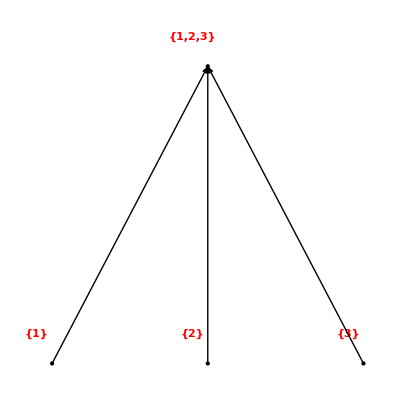

```mathematica
A={{1},{2},{3}, {1,2,3}};
R={{{1},{1}},{{3},{3}},{{2},{2}}, {{1},{1,2,3}}, {{2},{1,2,3}}, {{3},{1,2,3}}, {{1,2,3},{1,2,3}}};
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];B=A;t1=1;nivel=0;While[B≠{},minimales={};nivel++;Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False],{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,
{n1,1,Length[B]}];
B=Complement[B,minimales];
]
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];R1={};
Do[
Do[
If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,
R1=Union[R1,{R[[k1]]}];
];
,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];Do[t1++;puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2),{k1,1,cont}],
{j1,1,tabla[[Length[A],1]]}];Coord[elem_]:=Do[If[elem==tabla[[h1,2]],
Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];Do[Coord[A[[i1]]],{i1,1,Length[A]}];Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];
,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

```mathematica
b)Determinar los máximos,mínimos,elementos maximales y minimales.
```

```mathematica
A={1,3,5};
R={{1,1},{1,3},{1,5},{3,3},{5,5}};
maximo={};Do[maxi=True;Do[If[Intersection[{{A[[m]],A[[n]]}},R]=={},maxi=False],{m,1,Length[A]}];If[maxi,AppendTo[maximo,A[[n]]]];,{n,1,Length[A]}];If[maximo=={},Print["No tiene máximo"],Print["Máximo: ",maximo[[1]]]]

minimo={};Do[mini=True;Do[If[Intersection[{{A[[n]],A[[m]]}},R]=={},mini=False],{m,1,Length[A]}];If[mini,AppendTo[minimo,A[[n]]]];,{n,1,Length[A]}];If[minimo=={},Print["No tiene mínimo"],Print["Mínimo: ",minimo[[1]]]]

maximales={};Do[maximal=True;Do[If[Intersection[{{A[[n]],A[[m]]}},R]≠{}&&n≠m,maximal=False],{m,1,Length[A]}];If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];Print["Maximales: ",maximales]

minimales={};Do[minimal=True;Do[If[Intersection[{{A[[m]],A[[n]]}},R]≠{}&&n≠m,minimal=False],{m,1,Length[A]}];If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];Print["Minimales: ",minimales]
```

No tiene máximo

Mínimo: 1

Maximales: {3,5}

Minimales: {1}

```mathematica
c)Determinar las cotas superiores e inferiores,supremo e ínfimo de B en A.
```

```mathematica
A= {1,2,3,4,5};
B={1,3,5};
R={{1,1},{1,3},{1,5},{3,3},{5,5}};
cotassuperiores={};Do[csuper=True;Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False],{m,1,Length[B]}];If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];If[cotassuperiores=={},Print["No hay cotas superiores"],Print["Cotas superiores: ",cotassuperiores];supremo={};Do[mini=True;Do[If[Intersection[{{cotassuperiores[[n]],cotassuperiores[[m]]}},R]=={},mini=False],{m,1,Length[cotassuperiores]}];If[mini,AppendTo[supremo,cotassuperiores[[n]]]];,{n,1,Length[cotassuperiores]}];If[supremo=={},Print["No tiene supremo"],Print["Supremo: ",supremo[[1]]]]];

cotasinferiores={};Do[cinfer=True;Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False],{m,1,Length[B]}];If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];If[cotasinferiores=={},Print["No hay cotas inferiores"],Print["Cotas inferiores: ",cotasinferiores];infimo={};Do[maxi=True;Do[If[Intersection[{{cotasinferiores[[m]],cotasinferiores[[n]]}},R]=={},maxi=False],{m,1,Length[cotasinferiores]}];If[maxi,AppendTo[infimo,cotasinferiores[[n]]]];,{n,1,Length[cotasinferiores]}];If[infimo=={},Print["No tiene ínfimo"],Print["Ínfimo: ",infimo[[1]]]]];
```

No hay cotas superiores

Cotas inferiores: {1}

Ínfimo: 1